1

Introduction

## Models and Basic Concepts

### Introduction to Econometrics

Econometrics deals with estimating relationships between variables in many different settings. They help understand theoretical relationships between different variables and also provide a useful analytical platform for policy analysis and decision making.

Each application of Econometrics involves a few steps:

The formulation of a model

The estimation of unknown parameters

The testing of hypothesis

Prediction of future events using the model

### Formulation of a Model

The formulation step usually begins with a mental exercise where the econometrician uses theory and other practical considerations in deciding which Variables would be useful to include in the model.

Think of Consumer Demand Theory. We have consumers who are trying to maximize their utility subject to a budget constraint. The solution to this problem will yield a demand function for each good being considered.

#### Classification of Variables

Endogenous Variables (dependent): These are the variables you are trying to explain in your model.  (the are the “end...” goal in your modelling process

Exogenous Variables (independent): These are the Variables you are using in your model to try and explain the endogenous variables.

#### Representation of Models

Structural Representation: This is a mathematical representation of a hypothesized model (developed using economic theory) representing the endogenous and exogenous variables contained in your model.

Demand:Q_t = β_1+β_2 P_t + γ_1 Y_1+ϵ_(1t)
Supply: Q_t = β_3+β_4 P_t+γ_2 w_t+ϵ_(2t)

Reduced Form Representation: Here you express the endogenous variable by itself on the left side of the equation and the exogenous variables all on the right side of the equation.

P_t = (β_3-β_1)/(β_2-β_4)+γ_2/(β_2-β_4)w_t+γ_1/(β_2-β_4)Y_1+(ϵ_(1t)-ϵ_(2t))/(1-β_2)
Q_t = (-β_2 β_4)/(β_2-β_4)+(β_2 γ_2)/(β_2-β_4)w_t-(β_4 γ_1)/(β_2-β_4)Y_t+(β_2 ϵ_(1t)-β_4 ϵ_(2t))/(β_2-β_4)

### Estimation of Unknown Parameters

After you have written your model in Reduced Form the coefficients for the variables in the model are referred to as parameters and their values are usually unknown. The focus of this next step in the model creation process will be to fine adequate estimated for these parameters. The notation of β̂ will be used to represent an estimator for the unknown parameter β in the model.

Estimator: An estimator is a function or algorithm that one follows to produce an estimated value for a parameter.

### Hypothesis Testing

After you have come up with estimates for unknown parameters you may want to determine how important particular variables are.08 with regards to the overall explanatory power of your model. To do this you will need to have a knowledge of the distribution (density or pdf) of the estimator under a certain hypothesis.

H_0: β_2=0

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,2],x]],{x,-6,6},Filling->Axis,Ticks->False]
```

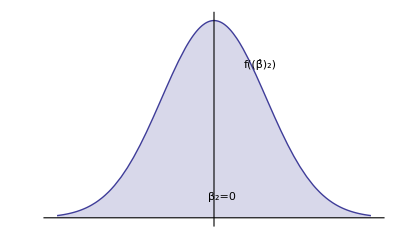

### Prediction

After your model has been formulated, estimated, and tested you usually want to use it to predict certain values for your endogenous variable using particular Variables for exogenous variables.

If your model was Y = β_1+β_2 X  you could plug in an interesting value (X*) for X and produce a corresponding Y value (Y*). You should remember that there is a zero probability of Y being exactly  Y*, but you will be able to establish some sort of confidence interval for the true value of Y.

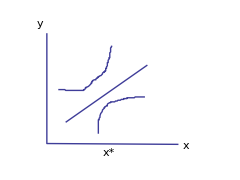

## Data

Often the models you create using econometric principles are influenced/limited by both the model presented AND the data used in the estimation of the parameters in the model.

### Data Characteristics

#### Quantitative-Qualitative

Quantitative Variables measure quantities such as price, sales volume, or income.

Qualitative Variables are used to model “either/or” situations and are usually associated with membership in a particular group.

#### Time Series, Cross Sectional, Pooled Data

Time Series Data: Measures a particular variable over successive time periods (annual, quarterly, weekly...)

Cross Seasonal Data: Measures a particular variable at a given point in time for different entities. An example would be the price of gas at a particular time at different gas station.

Pooled or Merged Cross Sectional/Time Series Data(Panel Data): This is used when you have cross sectional data sources all measured over time. You could compare  the average gas price in all states for a series of years. (the cross sectional data is the prices in the same year in different states and the time series is the data for one state in different years).

#### Non-Experimental and Experimental Data

Non-Experimental: This type of data is drawn from a system that is not subject to experimental control .

Experimental:  Data collected by experiment. This is where the individual has the ability to control for certain factors in the data.

### Data Problems

There are many different things that could cause problems in your data. Among them are that you simply don’t have enough data, the idea of mulicolinearity (different variables move together and influence each other), and the fact that all measured data is subject to uncertainty and error .

2

Simple Regression - The Classical Linear Regression Model

## Introduction

The main model we will be working with can be described mathematically as follows: Y_t=  β_1+β_2 X_t+ϵ_t

Population Regression Line (PRL or PRF): This is the function that is defined by our model, assuming the error terms are zero. Mathematically it is Y_t = β_1+β_2 X_t.

True Random Disturbance or Error Term This is how far off our models predicting of a point is from the actual data.

Below we will see a graphical representation of a PRL, the data points that could have produced this PRL, and a marker showing the error terms.

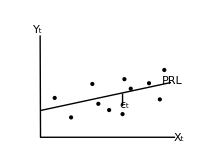

Population Regression Function (PRF): The regression function is defined as the PRL + error terms. Mathematically this is Y_t = β_1+β_2 X_t+ϵ_t

Sample Regression Function (SRF): This is the estimator of the population regression line and we will use β̂ for the estimated one and β for the actual . Mathematically this is (Ŷ)_t = (β̂)_1+(β̂)_2 X_t+e_t

Estimated Random Disturbance (residual): This is the estimate for the actual random disturbance and is e_t instead of ϵ_t

## Parameter Estimators

We are often presented with a set of (x,y) data pairs and told to estimate a linear relationship between them. In doing this we will have to find a reasonable estimate for a slope constant and also for an intercept constant.

We now have the question of how should we find (β̂)_1 and (β̂)_2 (the estimates for β_1 and β_2)? We know that we are going to want to minimize the distance from our regression line and from the actual data points (the further you are away, the worse your model did at predicting the appropriate value of y for a given x). Below are 5 possible methods for minimizing this distance (we will only use two of them: OLS and MM):

minimize Vertical distances: 1= Min[ ∑e_t] (this one has no unique solution because any line that passes through (x̄,ȳ) yields ∑e_t= 0

Min[ ∑e_t^2] this is the OLS

min ∑|e|^p (when p=2 we have OLS, when p=1 we have least absolute deviations (LAD)

min ∑(horizontal (distances))^2

### Derivation of Least Squares Estimators (OLS)

Sum of Squared errors: The sum of the squares of the vertical distances between Y_t and the Sample regression line is called the Sum of Squared Errors (SEE). The mathematical representation of this is SS = ∑(e^2)_t = ∑(Y_t - (β̂)_1-(β̂)_2 X_t)^2

```mathematica
Plot3D[{(x)^2+(y)^2+2,-(x-1)^2-y^2},{x,-2,2},{y,-2,2},PlotRange->{0,6},BoxRatios->Automatic,AxesLabel->{"β_1","β_2"},PlotLabel->"SSE"]
```

-Graphics3D-

Our goal is to minimize the SEE with respect to β_1 and β_2. We will do this by taking partial derivatives with respect to those parameters and setting the resultant expressions =0

(∂SSE)/(∂β_1) = 2 ∑(Y_t - (β̂)_1-(β̂)_2 X_t)^1 (-1) =0
 = -2*(∑Y_t/n - nβ_1/n - β_2∑X_t/n = 0/n
 = y^- - (β̂)_1 - (β̂)_2 X_t = 0
β_1 = y^--(β̂)_2 X_t

(∂SSE)/(∂β_2) = 2 ∑(Y_t - (β̂)_1-(β̂)_2 X_t)^1 (-X_t)= 0
∑ Y_t X_t - (β̂)_1∑X_t - (β̂)_2∑X_t^2 = 0/-2
∑(e_t X_t) = 0

If we take the result we found in the equations above and plug the value for (β̂)_1 into the second equation and solve for β_2

∑ Y_t X_t - (β̂)_1∑X_t - (β̂)_2∑X_t^2 = 0/-2
∑ Y_t X_t - (Y^--(β̂)_2 X^-)∑X_t - (β̂)_2∑X_t^2 =0
∑ Y_t X_t-  Y^-∑X_t= (β̂)_2∑X_t^2-(β̂)_2 X^-∑X_t^2
∑ Y_t X_t - n Y^-X^- = (β̂)_2(∑X_t^2 - X^-∑X_t)
(β̂)_2 = (∑ Y_t X_t - n Y^-X^-)/(∑X_t^2 - X^-∑X_t) = (Cov(x,y))/(Var(x))

### Derivation of MLE Estimators

The basic idea behind maximum likelihood estimators (MLE) is that we are looking for the most likely values parameters will have under certain conditions. To do this for the linear regression model we will operate under A.1-A.5 (see below).

If that is the case then our model is Y_t = β_1+β_2 X_t+ϵ_t
(1) E(Y_t) = β_1+β_2 X_t
(2) Var(Y_t|x_t) = Var(β_1+β_2 X_t+ϵ_t| X_t) = σ^2 and we can say that Y_t~N[β_1+β_2 X_t; σ^2]

Keeping that in mind and recalling the pdf for a normal distribution we can say that f(Y_t|X_t) = (e^(-(Y_t-β_1+β_2 X_t)^2/2 σ^2))/(√(2π)√(σ^2))

Likelihood Function: The likelihood function (L) for a random sample is the product of the density functions for all points.

L =(Y, β_1,β_2,σ^2) = f(y_1)*f(y_2)*...*f(y_n) =  (e^(-∑(Y_t-β_1+β_2 X_t)^2/2 σ^2))/((2π)^(n/2)(σ^2)^(n/2))

Log Likelihood Function: The log likelihood function (l) for a random sample is the natural log of the Likelihood function (L)

l(Y,β_1,β_2,σ^2) = ln[L(Y,β_1,β_2,σ)]

l(Y,β_1,β_2,σ^2) = ln[L(Y,β_1,β_2,σ)]
= ∑_t ln(f(Y_t)
= -∑(Y_t-β_1+β_2 X_t)^2/2 σ^2-n/2 ln(2π)- n/2 ln(σ^2)

Now we will use the above maximize the log likelihood function subject to our β’s by taking partial derivatives and setting them =0

(∂l)/(∂β_1) = -1/(2 σ^2)(∂SSE)/(∂β_1) =0
(∂l)/(∂β_2) = -1/(2 σ^2)(∂SSE)/(∂β_2) = 0
(∂l)/(∂σ^2) = SSE/2((σ̂)^2)^-2-n/2 1/(σ̂)^2=0

Notice that these are the first two are the exact same equations that allowed us to find the OLS estimates (the constant divides through and is wiped out be zero and we just differentiate the SSE). The third is just saying that we are minimizing the variance σ^2which was our other normal equation in finding the OLS estimators.

## Properties of OLS estimators

### The Five Assumptions (A.1-A.5)

(A.1): ϵ_tare normally distributed

(A.2): E(ϵ_t|X_t) = 0

(A.3): Homoskedasticity: Var(ϵ_t|X_t)=σ_t^2 = σ^2, for all t

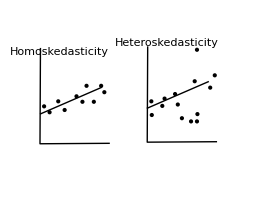

(A.4): No Autocorrelation: Cov(ϵ_t ϵ_s) = 0 t≠s

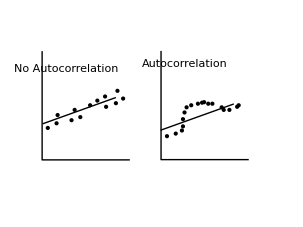

(A.5):  X’s are non-stochastic or in other words the X’s and the ϵ’s are not statistically correlated.

### The Two models (Classical Linear, and Classical Normal Linear)

#### Classical Linear Regression Model (A.2-A.5)

##### Properties

The β̂'s are unbiased: E((β̂)_i) = β_i

The β̂'s are consistent: Var((β̂)_i)-> 0 as n->∞

They have the minimum variable of all linear unbiased estimators (THE ARE BLUE)

OLS≠MLE

They are not normally distributed and therefore t and f stats are not exact.

#### Classical Normal Liner Regression Model (A.1-A.5)

##### Properties

The β̂'s are unbiased: E((β̂)_i) = β_i

The β̂'s are consistent: Var((β̂)_i)-> 0 as n->∞

They have the minimum variable of ALL unbiased estimators (THE ARE BLUE, and more)

OLS=MLE

They ARE  normally distributed and therefore t and f stats are not exact.

## Distribution of Estimators

The theoretical groundwork for being able to talk about the distribution of our estimators is that the β’s are functions of the Y’s (which are random variables). Because the β’s are functions of random variables, they themselves are also random variables with the same distribution as the y’s. That being said we can talk about the Expected Value, Variance, and distribution of the β’s.

σ_β_2^2 = σ^2/(∑(x_t-x^-)^2) = σ^2/(Var(x))
σ_(β_1^2)=  σ^2(1/n+((X^-)^2)/(∑(X_t-X^-)^2))=σ^2/n+X^-(σ^2)_β_2

There are a number of things that might affect the variance of your estimators. Some of the things that actually improve the precision of your estimators (reduce variance) are having less spread out data and having more data.

### Review up to this point

The model we are looking at is Y_t = β_1+β_2 X_t+ϵ_tand we follow A.1-A,.5 (see above)

The unknown parameters we want to estimate are β_1,β_(2,)and σ^2

The Estimators are given as follows: β_(1:)(β̂)_1 = Y^--(β̂)_2 X^-
β_(2:)(β̂)_2 = (∑(X_t-X^-)(Y_t-Y^-))/(∑(X_t-X^-)2)=(∑ Y_t X_t - n Y^-X^-)/(∑X_t^2 - X^-∑X_t) = (Cov(x,y))/(Var(x))
σ^2:   s^2 = ∑((e^2)_t)/(n-2) = (∑(Y_t-β_1-β_2 X_t)^2)/(n-2)  =SEE/(n-2)

The distributions of the estimators are as follows: (β̂)_1~ N[β_1,(σ^2)_β_1=σ^2/n+X^-(σ^2)_β_2]
(β̂)_2 ~N[β_2,(σ^2)_β_2 = σ^2/(∑(x_t-x^-)^2)]

## Statistical Inference (Descriptive Statistics and Hypothesis Testing)

For this section we assume that A.1-A.5 are valid.

One hypothesis that we might be concerned with is H_0:β_2=0 or that our model is just the intercept plus the error. We hope this is wrong but we could test it. (We would use either a Z stat that corresponds to a standard normal distribution or a t stat that corresponds to a t distribution. THE ONLY WAY TO USE A Z STAT is if we know the actual variance for the parameter we are testing. This hardly ever happens so we almost always use the t statistic.)

Z=(β̂-β^0)/σ_β~N[0,1]
t = (β̂-β^0)/s_β~t[n-2] And here β^0 is what we find on the right and side of H_0 (in our example above β^0=0.)

### The Coefficient of Determination (R^2)

The coefficient of determination measures the fraction of the total sum of squares error “explained” by the regression model . Look at the diagram below to see what SSE, SSR and SST are.

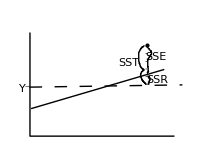

SST=∑(Y_t-Y^-)^2 =∑(Y_t-(Ŷ)_t+(Ŷ)_t-Y^-)^2  
= ∑(Y_t-Y^-)^2 + ∑(Ŷ-Y^-)^2+ 0 (if OLS use used cross terms=0)
= ∑(e^2)_t+∑(Ŷ-Y^-)^2 = SSE + SSR

R^2 = SSR/SSE = 1-SSE/SST

We should note that increasing the number of parameters (n) will not change the SST, but it will decrease the SSE as long as the coefficient for that parameter is not zero. This will result in R^2 always going up or staying the same if you add an additional parameter.

### ANOVA

In the following table K= number of β’s (including intercept!), n is the number of observations

Source of Variation | SS_ | d.f. | MSE
Model
Error | SSR
SSE | K-1
n-K | SSR/(K-1)
SSE/(n-K)
Total | SST | n-1 | SST/n-1

From the ANOVA table we can take the ratio between (2,4) and (3,4) and produce an f statistic. The hypothesis that corresponds to that statistic is that all slope β’s =0.

(SSR/(K-1))/(SSE/(n-K))`F[K-1,n-K] ... H_0: β_2= ...= β_k= 0

## Prediction/Forecasting

We have just discovered that Y~N[β_1+β_2 X_t, (σ^2)_(Ŷ)]  (note we can estimate  (σ^2)_(Ŷ) by (s^2)_(Ŷ) =s^2/n +(X_t-X^-)^2(s^2)_((β̂)_2))

Knowing this we can then create confidence intervals for acceptable values of our estimate of Y, Ŷ, by  saying that Ŷ ±t_c s_y, t_c=t_(α/2)(n-2)

With forecasting we are more concerned with finding the confidence intervals for the actual value of Y_t instead of the expected value of Y_tas shown above. To to this we need to talk about the Forecast Error (FE)

FE=Y_t-(Ŷ)_t
E(FE) = 0
σ_FE^2 = Var(FE|Y) = σ^2+σ_y^2
(s^2)_FE= (s^2)_(Ŷ)+s^2

To find the confidence intervals for the Actual Y_t we do this

Y_t±t*s_FE

## Functional Forms

### Transformable Models

#### Log-Log or Double Log Model

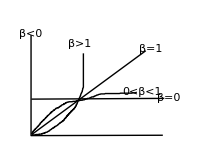

Y_t=AX_t^β ϵ_t
dY/dX=Aβx^(β-1)
η_(Y,X) = dy/dx*x/y = β

You can estimate this with OLS by estimating the model: ln(y) = Ln(a) + βln(x) + ln(ϵt) (reg ly lx)

#### Semi-Log Models

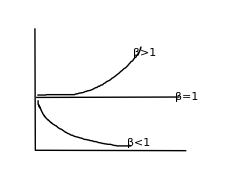

Y_t = Aβ^x_t ϵ_t
dy/dx = Y_t ln(β)
η_(y,x) = X*ln(β)

You can estimate this model by ln(y) = ln(A) + ln(β)*x+ln(ϵ) (reg ly x)

#### Reciprocal Transformations

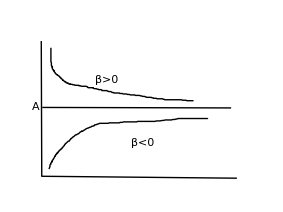

Y_t = A+β/x_t+ϵ_t
dy/dx = -β/x^2
η_(y,x) =-β/(xy)
You can estimate this model by saying Z = 1/x and regressing y = A+βZ+ϵ (reg y z)

#### Logarithmic Reciprocal Transformations

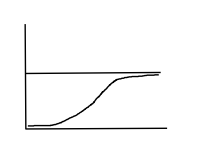

Y_t = e^(A-B/X+ϵ_t)
dy/dx =-βy/x^2
η_(y,x) = β/x

You can estimate this using OLS by saying ln(y) = A- β/x + ϵ then making the substitution Z = 1/x (reg ly Z)

#### Polynomials

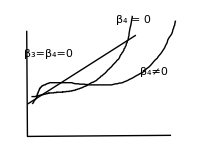

y=  β_1+β_(2x)+β_3 x^2+β_4 x^3

3

Classical Normal Linear Regression Model with k Independent Variables

## Basic Concepts

We are now moving out of scalar land and into matrices and vectors. For that reason will have to redefine some things.

y = (y_1
y_2
...
y_n) E(y) = (E(y_1)
E(y_2)
...
E(y_n)) Var(y) = (Var(y_1) | Cov(y_1 y_2) | ... | Cov(y_1,y_n)
Cov(y_2,y_1) | Var(y_2) | ... | Cov(y_2,y_n)
... | ... | ... | ...
Cov(y_n,y_1) | Cov(y_n,y_2) | ... | Var(y_n))= (E(y))^T E(y) = Σ

This n x 1 vector is said to be distributed as a multivariate normal with a mean vector μ and a variance-Covariance matrix Σ (y ~ N[μ,Σ] )

If this is the case the probability density function (pdf = f) f = (e^(-1/2(y-μ)^T Σ^-1(y-μ)))/((2π)^(n/2)|Σ|^(n/2))where |Σ| = Det[Σ]

The Useful Theorem:  If y~N[μ_y,Σ_y] then Z = Ay~N[μ_z = Aμ_y, Σ_Z = AΣ_y A^T] where A is a matrix of constant. Proof Below

E(z) = E(Ay) = A E(y) = Aμ_y
Var (Z) = E((z-E(z))(z - E(z))
= E[(Ay - Aμ_y) (Ay -Aμ_y)^T]
= A E[(y - μ_y)(y- μ_y)]A^T
= A Σ_y A^T

## Basic Model

We are now going to spend a little bit of time extending the basic model we have been using to cases where we wish to have more than two parameters. In this case β_i is interpreted as the marginal effect of x_i on the expected value of y.

The model can be re-written as shown below.

y_1 = β_1 x_11+β_2 x_12+....+β_k x_(1k)+ϵ_1
y_2 = β_1 x_21+β_2 x_22+....+β_k x_(2k)+ϵ_2
...
y_n = β_1 x_n1+β_2 x_n2+....+β_k x_nk+ϵ_n

For simplicity we define y = (y_1
y_2
...
y_n) , X = (x_11 | ... | x_(1k)
x_21 | ... | x_(2k)
... | ... | ...
x_n1 | ... | x_nk) β = (β_1
β_2
...
β_k) and ϵ = (ϵ_1
ϵ_2
...
ϵ_3)

The idea of dimension s really important in matrix algebra so we will define the dimension of all these matrices. y:n×1  X: n×k    β: k×1  ϵ: n×1

Now the model described by the equations above reduces to y = Xβ + ϵ. (NOTE that if you want to include an intercept term you need to have a column of zeros at the beginning of X)

## Estimation

### Deriving the OLS estimator for β

y = Xβ + ϵ = ŷ+ϵ

SSE( β̂) = ∑e_t^2 = ϵ^T ϵ = (y- Xβ)^T(y - Xβ) = y'y-2β̂'X'y+β̂'X'X β̂

(∂SSE)/(∂β̂) = -2X'y+2X' OverHat[Xβ] = 0-> X' OverHat[Xβ] = X'y

β̂ = (X'X)^-1 X'y

### Deriving MLE Estimator for β

Recall that y ~ N[ Xβ, Σ = Iσ^2]

L(y, μ, Σ) = (e^(-1/2(y-Xβ)^T Σ^-1(y-Xβ)))/((2π)^(n/2)|Σ|^(n/2)) =  (e^(-1/(2 σ^2)(y-Xβ)^T(y-Xβ)))/((2π)^(n/2)|σ^2 I|^(n/2)) = (e^((y-Xβ)^T(y-Xβ)/2 σ^2))/((2π)^(n/2)(σ^2)^(n/2))

l (y,μ,Σ) = ln (L) = ((y-Xβ)^T(y-Xβ))/(2 σ^2)-n/2 ln(2π) - n/2 ln(σ^2) = (-1/σ^2)SSE -n/2 ln(2π) - n/2 ln(σ^2)

(∂l)/(∂β)= 1/(2(σ^Δ)^2)(-2X'y + 2(X'X)β^Δ)=0 (this is the same as above ((∂SSE)/(∂β̂)= 0))

(∂l)/(∂σ^2) = ((y-X β^Δ)^T(y-X β^Δ))/((2(σ^Δ)^2)^2)-n/2)1/((σ^Δ)^2)=0

### BLUE estimators β̂ and β^Δ (the Δ is MLE and the ^ is OLS)

There are a few properties these BLUE estimators have to have. They must be linear (β̃ = Ay), they must be unbiased (E(β̃) = AE(y) = AXβ) = β, thus AX= I), they must have minimum variance. Note that method of moments (MOM), MLE ,and OLS all lead to the same β estimator under assumptions A.1-A.5.

#### Derivation (proof) of Expected Value of β̃

E(β̃) = E(Ay) = AE(y) (X'X)^-1 X'E(y) =(X'X)^-1 X' (Xβ) =(X'X)^-1 X'X β = Iβ = β

#### Derivation (proof) of Variance (β)

Var(β)=AΣA' = A(σ^2 I)A'
= (X'X)^-1 X' (σ^2 I) ((X'X)^-1 X')'
= σ^2(X'X)^-1 X'I  X''((X'X)^-1)'
= σ^2(X'X)^-1 X'X''((X'X)^-1)
= (σ^2(X'X))^-1

## Distribution of Estimators

Remember again that under A.1-A.5  y ~ N[Xβ, σ^2 I] and that β̃ = β̂ = β^Δ = (X'X)^-1 X'y.

The normal theorem therefore says that β̃~N[Aμ_y, AΣA'] =N [AXβ, Aσ^2 IA] = N[β, (σ^2(X'X))^(-1]) where A = (X'X)^-1 X'.

An unbiased estimator for (σ^2(X'X))^-1 is (s^2(X'X))^-1 where s^2 = e'e/(n-k) and it ((n-k)s^2)/σ^2~ χ^(2(n-k))

## Statistical Inference

### The F statistic

The first question we should as when it comes to statistical inference is how much overall explanatory power does our model have? This can be tested using H_0: β_2= β_3=...= β_k =0. This hypothesis will yield the following F statistic. F =(SSR/(k-1))/(SSE/ (n-k)) = R^2/(1-R^2)((n-k)/(k-1))~F[(k-1),(n-k)]. This can easily be computed from the ANOVA table by remembering that the 2nd and 3rd entries of the last row are SSR/(k-1) and SSE/ (n-k), respectively.

### T statistics

#### General Theory about T stats (THIS IS GOOD STUFF I ADDED!)

Whenever we have a hypothesis we want to test we would set it up like this H_(0:)(θ̂)_i = θ_guess

To test this hypothesis we would just need to say that ((θ̂)_i-θ_guess)/s_θ_i~ t(n-k)

We could test another hypothesis: H_0: θ_i=θ_j  -> θ_i-θ_j =0. This would lead to (θ_i-θ_j-0)/(√((s^2)_θ_i+(s^2)_θ_j)+2Cov(θ_i,θ_j))~t(n-k)

### Other Tests

Above we talked about testing the overall explanatory power of our model (the f stat), testing individual parameters or linear combinations of parameters (t-stats). Now we want to talk about a few other tests that can be used to test our model. The main idea behind this is that if a hypothesis about a particular variable is accurate imposing those hypothesis on our model shouldn’t effect R^2, SSE, or log-likelihoodsvery much.

There are a few basic steps to doing this:

Test the model without imposing any constraints

Estimate the same model, but this time with the constraints. Collected any additional data you might need to perform tests.

Compare results from the two models.

### Chow test

In this case we will look at the R^2values and compare them in a ratio using an F statistic. Note that R, SSE without a * are before the restrictions and if they have a * are after the restrictions.

F= ((SSE*-SSE)/r)/((SSE)/(n-k))= (R^2-R^(2*))/(1-R^2)(n-k)/r~F(r,(n-k)) where r = # of restrictions imposed on model.

### The Likelihood ratio (LR) test

The theory or idea behind this is about he same, but instead of focusing on the R^2 or SSE it focuses on the log likelihood value l.

If your hypothesis wasn't very good you should see a rather large drop in l. On the other hand if your hypothesis is really good you should see very little change.

LR = 2 (l-l*)  = (SSE^*- SSE)/σ^2 = n ln(1/(1-R^2)) = -nln(1-R^2)~ χ^2(r), again r is the number of restrictions.

## Stepwise Regression

Stepwise regression is used when trying to determine which variables or parameters to include when regressing a model. It isn’t theoretical at all (at least not economic theory) and you add or remove variables to see if the statistical effect is desirable.

There are two types of stepwise regression- forward and backwards.

In forwards regression you are add one independent variable at a time to see if it is statistically significant. If it is you keep it and move on to another variable. You should be aware that adding different variables to a model causes significance of older variables to change so you not only have to check significance of the added Variables each time, but also all surviving Variables.

In backwards stepwise regression you will do just the opposite. You start by doing the regression with all independent variables included and then you try to delete them one at time to see if it makes your model better or worse.

## Forecasting

Forecasting deals with trying to use data you already have to create a model and then use that model to predict values of an independent variables given certain values for independent variables.

Remember from before that the Forecast Error FE is given by FE= y_t-(ŷ)_t.

There are at least 4 things that will contribute to FE: having the wrong functional form for your model, random disturbance (error), uncertainty about the true values for β, and uncertainty about X.

If the problem is the existence of random disturbance (ϵ) you realize that FE= y_t-(ŷ)_t = y_t-F(X_t β) = ϵ_t and (σ^2)_FE = Variance (FE) = Var(ϵ_t) = σ^2. In this case the confidence intervals for y_t can be constructed y_t= +F(X_t β)±t_(α/2)σ

If the problem is uncertainty about β ASK JESSE AND LANCE FOR THEIR NOTES ON SECTION III PG. 33

4

Miscellaneous Topics - multicolinearity and Dummy Variables.

## multicolinearity

### Introduction/Review

Remember that in the model y = Xβ + ϵ the OLS estimator for β̂ = (X'X)^-1 X'y. As long as the columns of X are independent (the parameters are not related to each other) (X'X)^-1 will exist and you will be able to find a value for β. If any of those columns, however, can be expressed as a linear combination of any other columns then (X'X)^-1 is not defined and we have problems finding β.

Correlation matrix = Cor (X) = (Cor (X_1,X_1) | Cor (X_1,X_2) | ... | Cor (X_1,X_k)
Cor (X_2,X_1) | Cor (X_2,X_2) | ... | Cor(X_2,X_k)
... | ... | ... | ...
Cor(X_k,X_1) | Cor(X_k,X_2) | ... | Cor(X_k, X_k)) = (1 | ρ_12 | ... | ρ_(1k)
ρ_21 | 1 | ... | ρ_(2k)
... | ... | ... | ...
ρ_k1 | ρ_k2 | ... | 1) Remember that 0 <  Cor(X,Y) < 1

If two variables are completely independent the Cor between them will be equal to 1. If they are exact linear combinations of one another the Cor between them will be 0. Both are extreme and not very common (especially the second where Cor=0).

Multicolinearity: We define this term as existing whenever Cor(X) <1. It almost always exists so we usually ask how bad is the multicolinearity rather than the question about its existence.

### Example with two explanatory variables

A model with two explanatory variables is written as follows: y_t = β_1+β_2 x_t2+β_3 x_t3+ϵ_t where t= 1,2,...,n

With this model σ_β_i^2 = σ^2/(n Var(X_i) (1-(ρ^2)_23)) where ρ_23 =Correllation^2(X_2,X_3).

The confidence intervals for (β̂)_i are given by (β̂)_i ±t_(α/2)s_β_i =(t_(α/2)( s^2/(n Var(X_i) (1-(ρ^2)_23))))^(1/2) where t_(α/2) = (β_i-β)/s_β_i (H_(0:)β_i = β)

We can see that there are other things besides ρ that effect σ^2 for each β. In order for us to focus on the effect multicolinearity on the variance of a particular β we need to define something called the Variance Inflation Factor (VIF)

Variance Inflation Factor (VIF): The Variance inflation factor is equal to 1/(1-(ρ^2)_23)and estimates how much the variance of an estimated parameter is effected by mulicolinearity. A high VIF means a larger effect on the variance of the estimate and it means you have more severe multicolinearity.

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[3,σ],x],{σ,{.75,1,2}}],{x,-6,9},Filling->Axis]
```

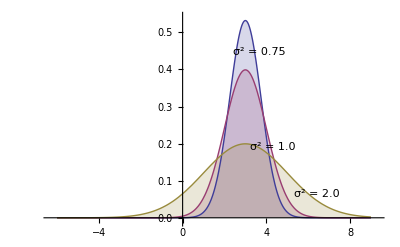

### Problems associated with multicolinearity

One of the problems associated with mulicolinearity is that you have a greater chance of assigning the wrong sign to a parameter coefficient. This could be really bad Because your model could say that advertising had a negative effect on sales, when that just doesn’t make much sense or you really need a new marketing department. You can see this in the example above. The most likely answer is that the coefficient is (+), but you can see that as σ^2  increases the chances of your model giving you a (-) increase.

Another problem is that you will have a hard time separating effects particular variables have on your dependent variable because things tend to move together.

Another issue is that you will end up computing much Smaller individual t statistics for the individual hypothesis that the β’s= 0.This is because as multicolinearity increases so does the variance and in computing t stats you divide by the variance.

The last issue is that you will often have very large or “significant” F statistics coupled with these small t stats. The F stat tells you that your model does well overall at predicting the dependent variable, but the small t’s tell you that none of the variables does a good job at it by themselves.

Another problem is that coefficients may be really sensitive to more data.

The corr may be close to 1 which means 1-ρ is close to zero.

Another thing to keep in mind is that even though you have all these potential problems, you still haven't violated A.1-A.5 and that means your β’s are still BLUE.

### Extending to more variables

If you extend to more variables you have the same s’s and β’s defined above but you need to know that ρ_i (for β_i) is equal to the R^2 term that you get when you call X_1 the dependent variable and do a regression with that and all the other variables as the independent variables.

This intuitively makes sense because if you have a high Correlation between one variable and the rest of them. A model where you try to predict the one using the others would be pretty good and therefore have a larger R^2.

### Proposed to solutions to mulicolinearity

Get more Data

Break the model down to it principle components by reducing correlated variables into linear combinations of those and then doing the regression.

Deleting a variable: sometimes all your Variables are different enough except for one or two that seem to be related to all of the other and therefore are the cause of multicolinearity.

Impose constraints on the parameters. This is pretty similar to the deleting a variable, but instead of saying that β=0 you have the flexibility to say the β = anything.  One good example is saying that you want constant returns to scale in a production function so your β’s corresponding to labor and capital need to sum to 1.

### Using Instrumental Variables to overcome endogenous regresses

Endogenous Regressor (ER):  An endogenous regressor is one that experiences feedback with the dependent variable. In other words, you have an endogenous regressor when changes in the regressor affect cause changes in the dependent variable and then that change causes further change in your ER.

The result of a regression including an endogenous regressor is that you will have biased and inconsistent β’s. this is a big deal because most of the statistical inference we have done breaks down and is not feasible.

Instrumental Variables: Instrumental variables are variables that you include in your regression that may explain an endogenous regressor. You do this so you can delete the ER from the model and hopefully not have the same feedback.

One example is this model: salary = β_1+β_2 education+β_3 experience. In this case education is your endogenous regressor Because as education goes up so does salary and that often motivates individuals to pursue more education. Some instrumental variables we could put in the model to replace education are mothersEducation, fathersEducation, proximityToUniversity...

## Dummy Variables

Binary Variables: Many variables that you might be interested in don’t have continuous values. Some may have only yes or no (like gender or age above a threshold). If this is the case you have a binary or dummy variable.

Dummy Variables: Other times you have more than just binary responses, but they are still at discrete levels (maybe age, work experience, or education). If this is the case what you will do is set up a dummy variable for each level in your category.

### Models with binary explanatory (independent) variables

An possible model for salary could include a binary variable for whether or not an individual is a college grad. A model for that could be Y_t = α_1+α_2 D_(1t)+ϵ_t where D is the dummy variable. If D = 1 the person graduated from college ,if D=0 they didn’t.

Another model talks about salary and whether or not you are a minority (D_1=1) and whether or not you are female (D_2 =1) Y_t = β_1 D_(1t)+β_2 D_(2t).

In each model you can infer that the coefficient in front of your dummy variable represents the impact on the dependent variable of having the dummy variable be 1.

Dummy Variable Trap: The Dummy Variable Trap is when regressing a model with “n” categories you include “n” slope coefficients. You can avoid the trap by simply leaving out an intercept coefficient or by including n-1 slope coefficients.

Interaction Term:  An interaction term is created by taking the product of two regressors. The Coefficient in front of that joint term is the additive marginal effect of the two regressors (in the case of two dummy variables it is the effect of belonging to both D=1 groups).

If you have things you would like to consider as dummy variables, but they don’t have just two states you will end up creating a binary variable for each level of distinction in that category (for example if you wanted each month would have 12 of them, each corresponding to a particular month).

### Models with binary dependent variables or limited dependent variables

Some good models that you would need binary dependent variables for are testing to see if a student will get in to graduate school, testing to see if someone is likely to Default on a loan, if someone will be married....

#### Linear Probability Model (LPM using OLS)

This model is presented as y_t = α+βx_t+ϵ_t where y=1 if a particular option is taken and 0 if otherwise.

If you do this regression the result will be describing the probability that the first choice was taken.

There are two main problems with this model: A.1 is violated (errors aren’t normal) so is A.5 (correlated error and x’s - heteroskedacity)!! Another problem is that your model is not bounded between 0,1 like it should be for a binary dependent variable.

reg y, X's
predict yhat
gen predy = yhat > .5
tabulate y predy

#### Qualitative Response Models

The idea behind both probit and logit are that they are bounded between 0 and 1 so they make much more sense to use in binary dependent variable case.

(□ | pdf:f(s;θ) | F(z) = ∫_(-∞)^z f(s;θ)
Normal
(Probit) | (e^(-s^2/2))/(√(2π)) | ∫_(-∞)^z (e^(-s^2/2))/(√(2π))
Logistic
(Logit) | e^-s/((1+e^-s)^2) | 1/(1+e^-z)) in all cases Z = Xβ = ŷ.

Marginal Effect of parameters:  The marginal effect of a parameter in a probit or logit model is (∂cdf)/(∂X_it) =β_i*(∂cdf)/(∂β)=  β_i*pdf. This is given to us with the Stata command “ margins, dydx(*) atmeans”